From the file ‘RefCurve_130143.txt.csv’.

```mathematica
SetDirectory["C:\\Users\\HILL\\Documents\\GitHub\\thesis\\figures\\oscillator"]
```

C:\Users\HILL\Documents\GitHub\thesis\figures\oscillator

```mathematica
data=Import["guiding.csv","Dataset",HeaderLines->1];
```

```mathematica
t=Normal[data[All,"t"]];
ch1=Normal[data[All,"ch1"]];
ch2=Normal[data[All,"ch2"]];
```

```mathematica
dT=0.04;thick=Directive[Thick];
```

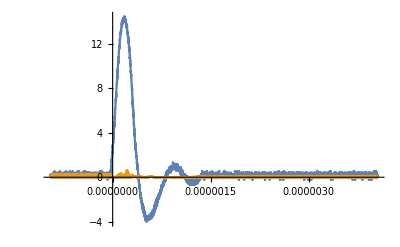

```mathematica
ListLinePlot[{Thread[{t,ch1}],Thread[{t,ch2}]},PlotRange->All]
```

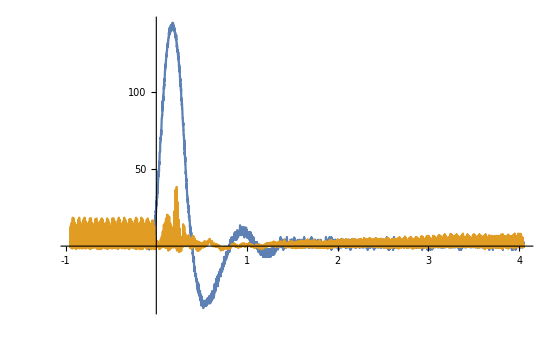

```mathematica
ListLinePlot[
{Thread[{t,ch1}],
Thread[{t,ch2*6}]},
PlotStyle->{Automatic,Automatic},
PlotRange->All,ImageSize->Small,
Ticks->{{{-1*^-6,-1,dT,thick},{1*^-6,1,dT,thick},{2*^-6,2,dT,thick},{3*^-6,3,dT,thick},{4*^-6,4,dT,thick}},{{5,50,dT,thick},{10,100,dT,thick},{15,150,dT,thick}}},
TicksStyle->Directive["Label", 20,Black]]
```

```mathematica
g1=ListLinePlot[Thread[{t,ch1}],PlotRange->All];
g2=ListLinePlot[Thread[{t,ch2}],PlotRange->All];
```

To do: Change the plot height to width ratio.

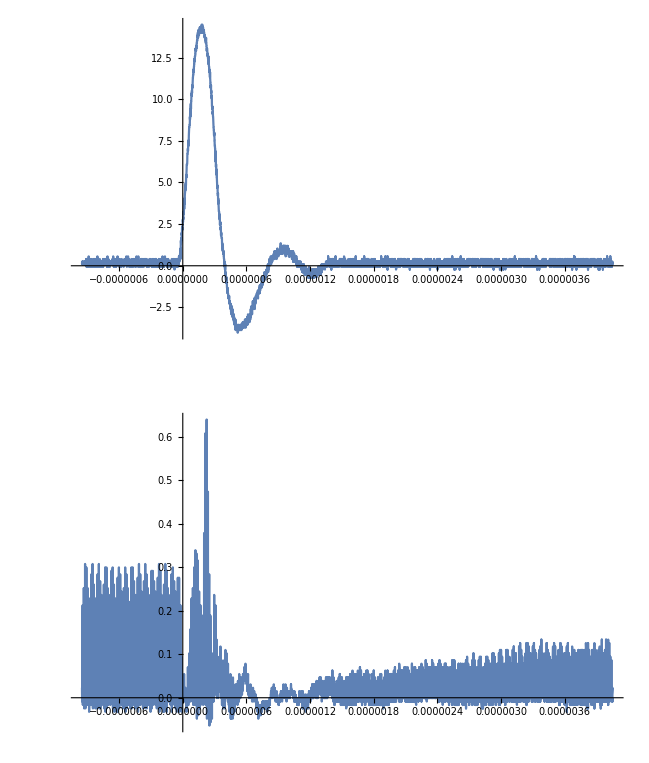

```mathematica
GraphicsColumn[{
g1,
g2
},
GridLines->{Table[102+4i,{i,4}],None},GridLinesStyle->{{Black,Dashed},None}]
```